## Fitnesses

```mathematica
θ[x_,thresh_]:=If[x<thresh,0,1];
πD[b_,num_,thresh_]:=b θ[num,thresh];
πC[b_,c_,num_,thresh_]:=πD[b,num,thresh]-c/num  θ[num,thresh]-c/thresh (1-θ[num,thresh]);
πintraD[d_,b_,c_,num_,ω_]:=b/d∑_(i=0)^(num-1) ω^i;
πintraC[d_,b_,c_,num_,ω_]:=πintraD[d,b,c,num,ω]-c;
```

```mathematica
Manipulate[GraphicsRow[{Plot[{∑_(k=0)^(d-1) (Binomial[d-1,k] x^k (1-x)^(d-1-k) πC[b,c,k+1,1]),∑_(k=0)^(d-1) (Binomial[d-1,k] x^k (1-x)^(d-1-k) πD[b,k,1])},{x,0,1},PlotStyle->{Blue,{Red,Dashed}},Frame->True,AspectRatio->1,Filling->{1->{{2},{Directive[Lighter[Red],Opacity[0.6]],Directive[Lighter[Blue],Opacity[0.6]]}}},PlotLabel->"Interspecies dynamics"],Plot[{∑_(k=0)^(dintra-1) (Binomial[dintra-1,k] y^k (1-y)^(dintra-1-k) πintraC[dintra,bintra,cintra,k+1,ω]),∑_(k=0)^(dintra-1) (Binomial[dintra-1,k] y^k (1-y)^(dintra-1-k) πintraD[dintra,bintra,cintra,k,ω])},{y,0,1},PlotStyle->{Blue,{Red,Dashed}},Frame->True,AspectRatio->1,Filling->{1->{{2},{Directive[Lighter[Red],Opacity[0.6]],Directive[Lighter[Blue],Opacity[0.6]]}}},PlotLabel->"Intraspecies dynamics"]}],
{{d,5},2,10,1},
{{b,2},2,12},
{{c,1},1,5},
{{dintra,5},2,10,1},
{{bintra,10},2,10},
{{cintra,3},1,5},
{{ω,0.75},0.1,2}]
```

## Dynamics

```mathematica
fD[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=p(∑_(k=0)^(d-1) (Binomial[d-1,k] x^k (1-x)^(d-1-k) πD[b,k,thresh]))+(1-p)(∑_(k=0)^(dintra-1) (Binomial[dintra-1,k] y^k (1-y)^(dintra-1-k) πintraD[dintra,bintra,cintra,k,ω]));
fC[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=p(∑_(k=0)^(d-1) (Binomial[d-1,k] x^k (1-x)^(d-1-k) πC[b,c,k+1,thresh]))+(1-p)(∑_(k=0)^(dintra-1) (Binomial[dintra-1,k] y^k (1-y)^(dintra-1-k) πintraC[dintra,bintra,cintra,k+1,ω]));
fbar1[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=x fC[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p]+(1-x)fD[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p];
fbar2[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,ω_,p_]:=y fC[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p]+(1-y)fD[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p];
xdot[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,m_,ω_,p_]:=m x (1-x) (fC[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p] - fD[d,dintra,y,x,b,c,bintra,cintra,thresh,ω,p]);
ydot[d_,dintra_,x_,y_,b_,c_,bintra_,cintra_,thresh_,n_,ω_,p_]:=n y (1-y)(fC[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p] - fD[d,dintra,x,y,b,c,bintra,cintra,thresh,ω,p]);
res[p_,q_,lim_]:=Quiet[NDSolve[{x'[t]== m x[t] (fC[d1,d1intra,y[t],x[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,prob] - fbar1[d1,d1intra,x[t],y[t],b,c,bintraforsp1,cintraforsp1,thresh1,ωforsp1,prob]),y'[t]==n y[t] (fC[d2,d2intra,x[t],y[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,prob] - fbar2[d2,d2intra,x[t],y[t],b,c,bintraforsp2,cintraforsp2,thresh2,ωforsp2,prob]),x[0]==p,y[0]==q},{x,y},{t,lim}]];
liseval[t_,rep_]:=Evaluate[{x[t],y[t]}/.rep];

gamea={3,3/4};
gameb={1,3/4};
gamec={1,4/3};
gamed={3,4/3};

d1=5;
d2=5;
d1intra=5;
d2intra=5;
thresh1=1;
thresh2=1;
b=3;
c=1;
bintraforsp1=10;
cintraforsp1=gameb⟦1⟧;
ωforsp1=gameb⟦2⟧//N;

bintraforsp2=10;
cintraforsp2=gameb⟦1⟧;
ωforsp2=gameb⟦2⟧//N;

m=1/8//N;
n=1;

prob=0.666;
lim=800;
```

ReplaceAll::reps: {rep} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Clear[blue,red,black];
blue={};
red={};
black={};
For[u=0.0,u≤1.0,u=u+0.01,For[v=0.0,v≤1.0,v=v+0.01,
If[
liseval[lim,res[u,v,lim]]⟦1⟧⟦1⟧>0.9999&&liseval[lim,res[u,v,lim]]⟦1⟧⟦2⟧<0.01,AppendTo[red,{u,v}],If[liseval[lim,res[u,v,lim]]⟦1⟧⟦1⟧<0.01&&liseval[lim,res[u,v,lim]]⟦1⟧⟦2⟧>0.9999,AppendTo[blue,{u,v}],AppendTo[black,{u,v}]]];
]]
```

```mathematica
ans=Solve[{xdot[d1,d1intra,x,y,b,c,bintraforsp1,cintraforsp1,thresh1,m,ωforsp1,prob]==0,ydot[d2,d2intra,x,y,b,c,bintraforsp2,cintraforsp2,thresh2,n,ωforsp2,prob]==0,xdot[d1,d1intra,x,y,b,c,bintraforsp1,cintraforsp1,thresh1,m,ωforsp1,prob]==ydot[d2,d2intra,x,y,b,c,bintraforsp2,cintraforsp2,thresh2,n,ωforsp2,prob]},{x,y}];
xlis={};
ylis={};
For[i=1,i≤Length[ans],i++,
For[j=1,j≤2,j++,
If[ans⟦i⟧⟦j⟧⟦1⟧==x,
temp=ans⟦i⟧⟦j⟧⟦2⟧//N;
If[Head[temp]==Real&&temp>0&&temp<1,AppendTo[xlis,temp]]
];
If[ans⟦i⟧⟦j⟧⟦1⟧==y,
temp=ans⟦i⟧⟦j⟧⟦2⟧//N;
If[Head[temp]==Real&&temp>0&&temp<1,AppendTo[ylis,temp]]
]
]
]
xlis=Flatten[Union[xlis]];
ylis=Flatten[Union[ylis]];

xplots=Table[ContourPlot[y==ylis⟦z⟧,{x,0,1},{y,0,1},AspectRatio->1,ContourStyle->{Blue,Thickness[0.003]}],{z,1,Length[ylis]}];
yplots=Table[ContourPlot[x==xlis⟦z⟧,{x,0,1},{y,0,1},AspectRatio->1,ContourStyle->{Red,Thickness[0.003]}],{z,1,Length[xlis]}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Greater::nord: Invalid comparison with 0.872959-3.12704 ⅈ attempted.

Less::nord: Invalid comparison with 0.872959-3.12704 ⅈ attempted.

Greater::nord: Invalid comparison with 0.872959+3.12704 ⅈ attempted.

Less::nord: Invalid comparison with 0.872959+3.12704 ⅈ attempted.

Greater::nord: Invalid comparison with 7.12704-3.12704 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Less::nord: Invalid comparison with 7.12704-3.12704 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

```mathematica
(*(*p1fun[d1_,d2_,b_,c_,thresh1_,thresh2_,m_,n_]:=ContourPlot[{ydot[d2,x,y,b,c,thresh2,n]==0,xdot[d1,x,y,b,c,thresh1,m]==0},{y,0,1},{x,0,1},ContourStyle->{{Thickness[0.009],Red},{Thickness[0.009],Blue}},Axes->False,Frame->True];*)
p2fun[d1_,d2_,d1intra_,d2intra_,b_,c_,thresh1_,thresh2_,m_,n_]:=StreamPlot[{
xdot[d1,d1intra,x,y,b,c,bintraforsp1,cintraforsp1,thresh1,m,ωforsp1,prob],ydot[d2,d2intra,x,y,b,c,bintraforsp2,cintraforsp2,thresh2,n,ωforsp2,prob]},{x,0.0001,1},{y,0.0001,1},StreamScale->0.2,Axes->False,StreamPoints->30,StreamStyle->{"PinDart",Directive[Black,Thick]},Frame->True,PlotRange->{{-0.01,1.01},{-0.01,1.01}},StreamColorFunction->(Black&)];
(*diagonal=Plot[1-x,{x,0,1},PlotStyle->{Thickness[0.005],Green,Dashed},AspectRatio->1,Frame->True];*)
(*sep=ContourPlot[ydot[d2,x,y,b,c,thresh2,n]==xdot[d1,x,y,b,c,thresh1,m],{x,0,1},{y,0,1},ContourStyle->{Thickness[0.005],Green,Dashed}];*)*)
```

```mathematica
p2fun[d1_,d2_,d1intra_,d2intra_,b_,c_,thresh1_,thresh2_,m_,n_]:=StreamPlot[{
xdot[d1,d1intra,x,y,b,c,bintraforsp1,cintraforsp1,thresh1,m,ωforsp1,prob],ydot[d2,d2intra,x,y,b,c,bintraforsp2,cintraforsp2,thresh2,n,ωforsp2,prob]},{x,0.0001,1},{y,0.0001,1},StreamScale->0.2,Axes->False,StreamPoints->30,StreamStyle->{"PinDart",Directive[Black,Thick]},Frame->True,PlotRange->{{-0.01,1.01},{-0.01,1.01}},StreamColorFunction->(Black&)]
```

```mathematica
g1=ListPlot[{blue,red,black},PlotStyle->{Lighter[Blue,0.4],Lighter[Red,0.4],Lighter[Gray,0.7]},AspectRatio->1,Frame->True,PlotRange->{{-0.01,1.01},{-0.01,1.01}}];
```

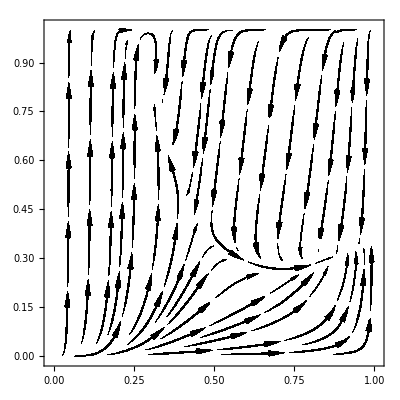

```mathematica
p2fun[d1,d2,d1intra,d2intra,b,c,thresh1,thresh2,m,n]
```

```mathematica
p2contour[d1_,d2_,d1intra_,d2intra_,b_,c_,thresh1_,thresh2_,m_,n_]:=ContourPlot[{
xdot[d1,d1intra,x,y,b,c,bintraforsp1,cintraforsp1,thresh1,m,ωforsp1,prob]==0.00,ydot[d2,d2intra,x,y,b,c,bintraforsp2,cintraforsp2,thresh2,n,ωforsp2,prob]==0.00},{x,0.001,0.99},{y,0.001,0.99},ContourStyle->{{Thickness[0.005],Blue},{Thickness[0.005],Red}}]
```

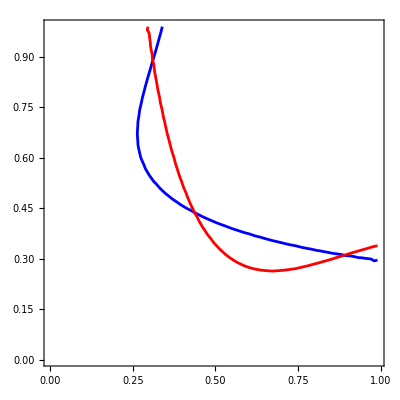

```mathematica
p2contour[d1,d2,d1intra,d2intra,b,c,thresh1,thresh2,m,n]
```

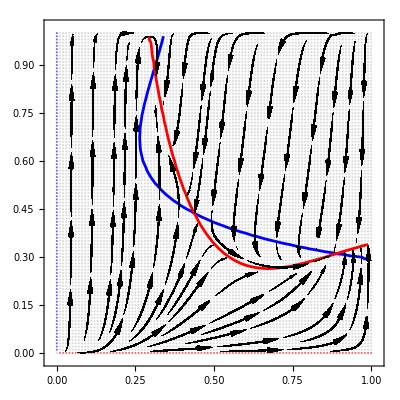

```mathematica
Show[g1,(*,p1fun[d1,d2,b,c,thresh1,thresh2,m,n],*)p2contour[d1,d2,d1intra,d2intra,b,c,thresh1,thresh2,m,n],p2fun[d1,d2,d1intra,d2intra,b,c,thresh1,thresh2,m,n](*,xplots,yplots*),Frame->True,FrameStyle->Thickness[0.0025],ImagePadding->17,PlotRange->{{-0.02,1.02},{-0.02,1.02}}]
```

```mathematica
(*Export["Untitled.pdf",%]*)
```